```mathematica
ClearAll["Global`*"]
```

```mathematica
(* GAPDH Kinetics with 30 mM Tris, 10 mM Arsenate, pH 8.5 by MW-KK 2020 *)(* NAD+ levels are 0.125; 0.250, and 0.500 mM *)
cGAP={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800};
v125={0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188};
v250={0.050,0.104,0.150,0.182,0.237,0.241,0.264,0.259,0.266,0.232};
v500={0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.310,0.334,0.322};
```

```mathematica
cGAP={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800};
v125={0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188};
```

```mathematica
iv125=1/v125
iv250=1/v250
iv500=1/v500
```

{25.641,10.5263,7.75194,5.84795,5.31915,5.49451,5.20833,4.85437,5.34759,5.31915}

{20.,9.61538,6.66667,5.49451,4.21941,4.14938,3.78788,3.861,3.7594,4.31034}

{22.7273,9.70874,6.21118,4.71698,3.7594,3.48432,3.41297,3.22581,2.99401,3.10559}

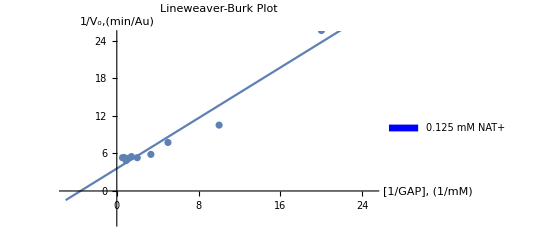

```mathematica
x9
```

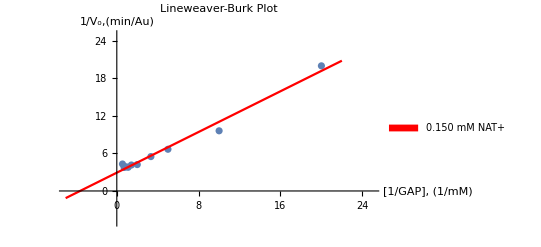

```mathematica
x10
```

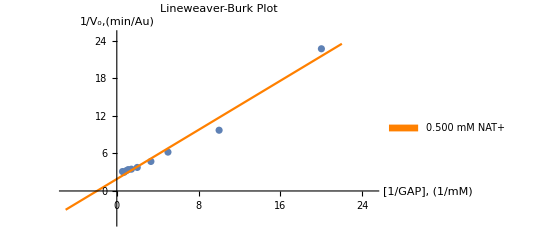

```mathematica
x11
```

```mathematica
Show[x9,x10,x11]
```

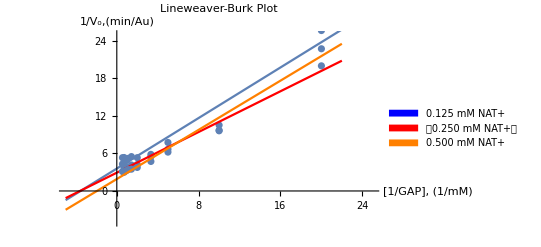

```mathematica
i125fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 3.58085 | 0.607896 | 5.89055 | 0.00036562
x | 1.00999 | 0.0823415 | 12.2658 | 1.81387×10^-6

```mathematica
i150fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.92184 | 0.280534 | 10.4153 | 6.2595×10^-6
x | 0.813407 | 0.0379992 | 21.4059 | 2.38719×10^-8

```mathematica
i500fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.90785 | 0.37391 | 5.10244 | 0.000927058
x | 0.982593 | 0.0506473 | 19.4007 | 5.17358×10^-8

```mathematica
?x9
```

```mathematica
?x10
```